```mathematica
schk=6*{17+15,17+1, 17+6}
overall={6,0,4}+{4,1,0}+schk
```

{192,108,138}

{202,109,142}

```mathematica
multivariateMul[n_]:=overall[[1]]*2^n;
univariateMul[n_]:=(54+3*Log[2,3]+15*n)*2^n;
breakeven= NSolve[multivariateMul[x]-univariateMul[x]==0,x]
```

{{x→9.54967}}

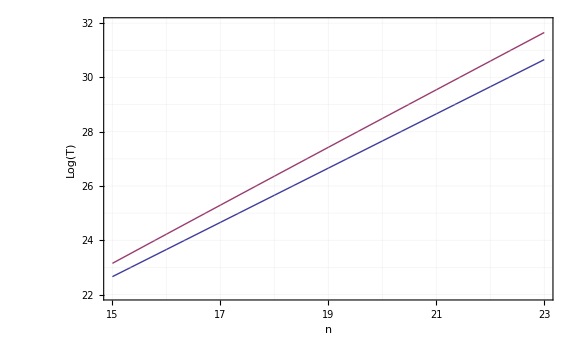

```mathematica
rangeX={15,23};
rangeY={Log[2,multivariateMul[First@rangeX]]//Floor, 
Log[2,univariateMul[Last@rangeX]]//Ceiling
};
Plot[
{Log[2,multivariateMul[n]],Log[2,univariateMul[n]]},
{n,First@rangeX, Last@rangeX},
AxesOrigin->{First@rangeX,First@rangeY},
PlotRange->{rangeX,rangeY},
GridLines->{Range@@rangeX, Range@@rangeY},
GridLinesStyle->Opacity[0.3],
Frame->True,
FrameTicks->{Range@@rangeX, Range@@rangeY,None,None},
FrameLabel->{"n","Log(T)"},
ImageSize->Large
]
```

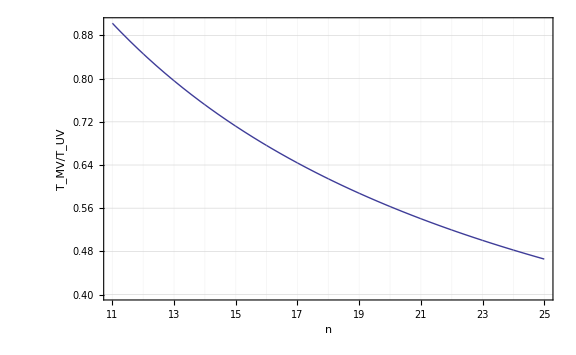

```mathematica
rangeX={11,25};
Plot[
(univariateMul[n]/multivariateMul[n])^(-1),
{n,First@rangeX, Last@rangeX},
AxesOrigin->{First@rangeX,0.4},
GridLines->{Range@@rangeX,Automatic},
GridLinesStyle->Opacity[0.3],
Frame->True,
FrameTicks->{Range@@rangeX, Automatic,None,None},
FrameLabel->{"n","T_MV/T_UV"},
ImageSize->Large
]
```